```mathematica
Quit
```

## Define flow

```mathematica
D[f[t,x],x]
2 a[t] x+b[t]
```

f^(0,1)[t,x]

2 x a[t]+b[t]

```mathematica
{vx[t_,x_,y_],vy[t_,x_,y_]}:={g[t,x,y],-g[t,y,x](2 a[t] x+b[t])};
```

```mathematica
a[t_]:=ϵ Sin[ω t];
b[t_]:=1-2 ϵ Sin[ω t];
f[t_,x_]:=a[t] x^2+b[t] x;
(*
{vx[t_,x_,y_],vy[t_,x_,y_]}:={-π A Sin[π f[t,x]] Cos[π y],-π A Cos[π f[t,x]] Sin[π y](2 a[t] x+b[t])};
{vx[t_,x_,y_],vy[t_,x_,y_]}:={-π A Sin[π f[t,x]] Sin[π y],-π A Cos[π f[t,x]] Cos[π y](2 a[t] x+b[t])};*)
g[t_,x_,y_]:=π A Sin[π f[t,x]]Cos[π f[t,y]](*D[f[t,x],x]*)
(*{vx[t_,x_,y_],vy[t_,x_,y_]}:={-g[t,x,y],-g[t,y,x](2 a[t] x+b[t])};*)

(* quad gyre *)
{vx[t_,x_,y_],vy[t_,x_,y_]}:={g[t,x,y],-g[t,y,x](2 a[t] x+b[t])};

(* double gyre *)
{vx[t_,x_,y_],vy[t_,x_,y_]}:={-π A Sin[π f[t,x]]Cos[π y],π A Cos[π f[t,x]]Sin[π y](2 a[t] x+b[t])};

params = {A->0.1,ϵ->0.1,ω->π/5};
```

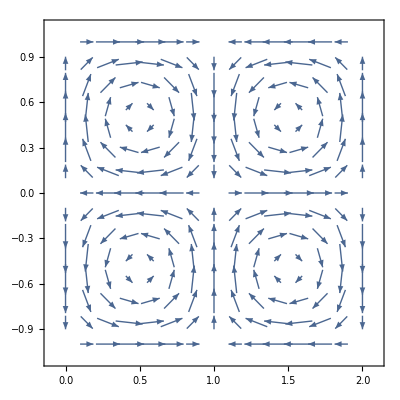

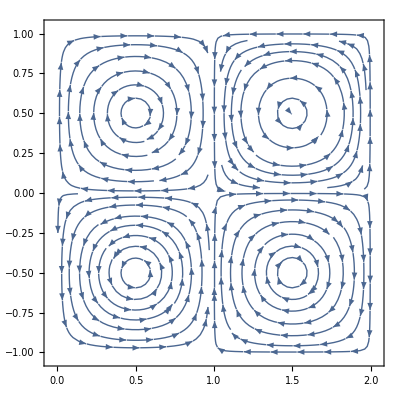

```mathematica
sys={vx[t,x,y],vy[t,x,y]}/.params/.t->0;
VectorPlot[sys,{x,0,2},{y,-1,1}]
StreamPlot[sys,{x,0,2},{y,-1,1}]
```

## Test cases

```mathematica
Remove[pathPlot]
```

```mathematica
Options[pathPlot]
```

{findFTLE`Private`streamPoints→20}

```mathematica
Eigenvalues[{{1,3.1},{3,2}}]
```

{4.59031,-1.59031}

```mathematica
Eigensystem[{{1,3.1},{3,2}}]
```

{{4.59031,-1.59031},{{-0.653533,-0.756898},{-0.767372,0.641203}}}

```mathematica
Eigenvectors[{{1,3.1},{3,2}}]
```

{{-0.653533,-0.756898},{-0.767372,0.641203}}

```mathematica
SetDirectory[NotebookDirectory[]]
<<lagrange2d.wl
RandomSeed[0];
params = {A->0.1,ϵ->0.25,ω->π/5};
```

### Plot pathlines

/Users/william/Documents/Research/fluid mathematica package

{a→5,n→100,seeds1→0}

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

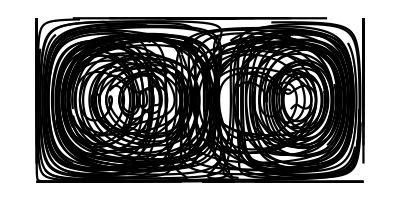

{n→20,n→100,seeds1→0}

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

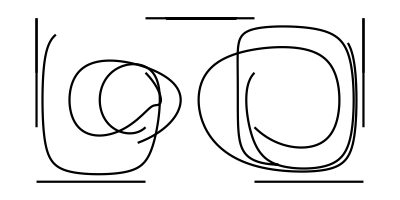

```mathematica
pathPlot[{vx[t,x,y],vy[t,x,y]}/.params,{x,0,2},{y,0,1},{t,0,15},(*{n->10},*)PlotStyle->Black,Axes->False]

pathPlot[{vx[t,x,y],vy[t,x,y]}/.params,{x,0,2},{y,0,1},{t,0,15},{n->20},PlotStyle->Black,Axes->False]
```

{seeds1→{{0.2,0.1},{0.201,0.101}},n→100,seeds1→0}

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

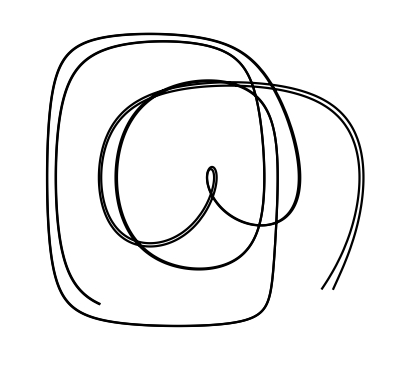

```mathematica
pathPlot[{vx[t,x,y],vy[t,x,y]}/.params,{x,0,2},{y,0,1},{t,0,45},{seeds1->{{.2,.1}, {.201,.101}}},PlotStyle->Black,Axes->False]
```

### Visualize advection of a blob

```mathematica
ptLocs=advectPoints[ 
makeMesh[{1.2,1.6},{.1,.5},50,50],
{vx[t,x,y],vy[t,x,y]}/.params,
{t,0,20},x,y];
im=Show[{
ListPlot[Flatten[{x[t],y[t]}/.ptLocs/.t->20,1],PlotStyle->Blue],
ListPlot[Flatten[{x[t],y[t]}/.ptLocs/.t->10,1],PlotStyle->Lighter[Blue,.6]]
},
PlotRange->{{0,2},{0,1}},AspectRatio->Automatic,Axes->False];
ImageReflect[ImageReflect[Image[im],Top],Left]
```

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

-Graphics-

### Visualize the field of maximal Lyapunov exponents

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

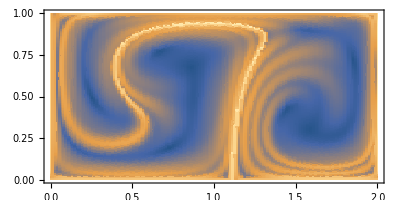

```mathematica
params =  {A->0.1,ϵ->0.25,ω->π/5};
ftleField=findMaxFTLEField[{vx[t,x,y],vy[t,x,y]}/.params,makeMesh[{0,2},{0,1},150,150],{t,0,10},x,y];
ListDensityPlot[ftleField,InterpolationOrder->0,AspectRatio->Automatic]
```

### Visualize the Kaplan-Yorke exponents

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

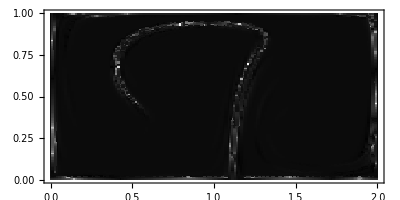

```mathematica
ftleVals=findFTLEField[{vx[t,x,y],vy[t,x,y]}/.params,makeMesh[{0,2},{0,1},150,150],{t,0,10},x,y];
kyVals=findKYDim[ftleVals];

signedLog=Sign[#]Log[1+Abs[#]]&; (* for visualization *)

ListDensityPlot[{#[[1]],#[[2]],signedLog[#[[3]]]}&/@kyVals,InterpolationOrder->0,AspectRatio->Automatic,PlotRange->All,ColorFunction->GrayLevel]
```

### Draw lines of maximal stretching

```mathematica
stretchVecsPositive=findStretchlines[{vx[t,x,y],vy[t,x,y]}/.params,makeMesh[{0,2},{0,1},100,100],{t,0,10},x,y,"Positive"];
stretchVecsNegative=findStretchlines[{vx[t,x,y],vy[t,x,y]}/.params,makeMesh[{0,2},{0,1},100,100],{t,0,10},x,y,"Negative"];
```

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

yes

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

yes

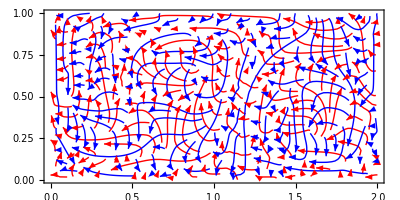

```mathematica
Show[{
ListStreamPlot[{{#[[1]],#[[2]]},#[[3]]}&/@stretchVecsPositive,AspectRatio->Automatic,PlotRange->All,StreamStyle->Red,StreamScale->{10,500,.005}],
ListStreamPlot[{{#[[1]],#[[2]]},#[[3]]}&/@stretchVecsNegative,AspectRatio->Automatic,PlotRange->All,StreamStyle->Blue,StreamScale->{10,500,.005}]
}]
```

Overlay on the FTLE field

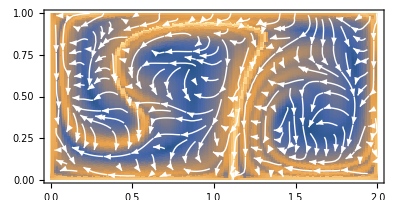

```mathematica
Show[
{
ListDensityPlot[ftleField,InterpolationOrder->0,AspectRatio->Automatic],
(*ListVectorPlot[{{#[[1]],#[[2]]},#[[3]]}&/@stretchVecs,AspectRatio->Automatic,PlotRange->All,VectorStyle->White]*)
ListStreamPlot[{{#[[1]],#[[2]]},#[[3]]}&/@stretchVecsPositive,AspectRatio->Automatic,PlotRange->All,StreamStyle->White]
}]
```

### Make video of a time-varying flow

## delete this

Need to fill in missing mesh points using nan-replacement interpolation so that i can then use higher-order interpolation

```mathematica
cleanedOutputs=cleanSquirmerTraj[simResults,tMax];
t0=0.0;
tf=5;
tf=10;
tf=75/2;
tf=tMax/2;
startPts=Evaluate[{x[t],y[t]}/.cleanedOutputs]/.t->t0;
stopPts = Evaluate[{x[t],y[t]}/.cleanedOutputs]/.t->tf;
startPts=startPts⟦1;;All,1,1;;All⟧;
stopPts=stopPts⟦1;;All,1,1;;All⟧;

(*For really big arrays, have to write these arrays to disk and then reload*)
(*Export["start.mx",startPts];
Export["stop.mx",stopPts];*)
```

```mathematica
(*
t0=0.0;
tf=5;
tf=10;
tf=75/2;
tf=25;

startPts=Import["start.mx"];
stopPts=Import["stop.mx"];*)

xMapPts=MapThread[{#1,#2}&,{startPts,Transpose[stopPts][[1]]}];
yMapPts=MapThread[{#1,#2}&,{startPts,Transpose[stopPts][[2]]}];

xMap = Interpolation[xMapPts];
yMap = Interpolation[yMapPts];
```

```mathematica
makeMap[trajList_,t0_,tf_]:=Module[{startPts,stopPts,xMapPts,yMapPts,xMap,yMap},
startPts=Evaluate[{x[t],y[t]}/.cleanedOutputs]/.t->t0;
stopPts = Evaluate[{x[t],y[t]}/.cleanedOutputs]/.t->tf;
startPts=startPts⟦1;;All,1,1;;All⟧;
stopPts=stopPts⟦1;;All,1,1;;All⟧;

startPts=Evaluate[{x[t],y[t]}/.cleanedOutputs]/.t->t0;
stopPts = Evaluate[{x[t],y[t]}/.cleanedOutputs]/.t->tf;
startPts=startPts⟦1;;All,1,1;;All⟧;
stopPts=stopPts⟦1;;All,1,1;;All⟧;

xMapPts=MapThread[{#1,#2}&,{startPts,Transpose[stopPts][[1]]}];
yMapPts=MapThread[{#1,#2}&,{startPts,Transpose[stopPts][[2]]}];
xMap = Interpolation[xMapPts];
yMap = Interpolation[yMapPts];
{xMap,yMap}

(*DeleteFile["startInner.mx"];*)
(*DeleteFile["stopInner.mx"];*)
]
```

```mathematica
t0=0.0;
tf=5;
tf=10;
tf=75/2;
tf=tMax;

startPts=Evaluate[{x[t],y[t]}/.cleanedOutputs]/.t->t0;
stopPts = Evaluate[{x[t],y[t]}/.cleanedOutputs]/.t->tf;
startPts=startPts⟦1;;All,1,1;;All⟧;
stopPts=stopPts⟦1;;All,1,1;;All⟧;

startPts=Evaluate[{x[t],y[t]}/.cleanedOutputs]/.t->t0;
stopPts = Evaluate[{x[t],y[t]}/.cleanedOutputs]/.t->tf;
startPts=startPts⟦1;;All,1,1;;All⟧;
stopPts=stopPts⟦1;;All,1,1;;All⟧;

(*For really big arrays, have to write these arrays to disk and then reload*)
(*Export["start.mx",startPts];
Export["stop.mx",stopPts];*)

(*For really big arrays, have to write these arrays to disk and then reload*)
(*Export["start.mx",startPts];
Export["stop.mx",stopPts];*)

xMapPts=MapThread[{#1,#2}&,{startPts,Transpose[stopPts][[1]]}];
yMapPts=MapThread[{#1,#2}&,{startPts,Transpose[stopPts][[2]]}];
xMap = Interpolation[xMapPts];
yMap = Interpolation[yMapPts];
```

{{1.,1.5},{1.×10^-14,0.5}}

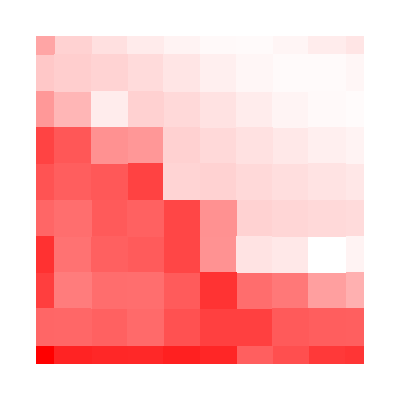

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
Needs["DivergentColorMaps`"]
fMat=Evaluate[{D[{xMap[p,q],yMap[p,q]},p],D[{xMap[p,q],yMap[p,q]},q]}];
(*Fmatrix[p_,q_]=MatrixPower[fMat,tMax/tf];*)
FtF[p_,q_]=MatrixPower[Transpose[fMat].fMat,tMax/tf];
ftle[x_,y_]:=1/Abs[tf-t0] Log[Sqrt@Max@Eigenvalues[FtF[x,y]]];
(*ftle[x_,y_]:=Max@Eigenvalues[FtF[x,y]];*)

{{xlo,xhi},{ylo,yhi}}=InterpolatingFunctionDomain[Head@fMat[[1,1]]]
(*ContourPlot[ftle[x,y],{x,xlo,xhi},{y,ylo,yhi}]
DensityPlot[ftle[x,y],{x,xlo,xhi},{y,ylo,yhi}]*)
ftleVals={#[[1]],#[[2]],ftle@@#}&/@startPts;
ftlePlot=ListDensityPlot[ftleVals,InterpolationOrder->0,(*ColorFunction->CoolToWarm*)ColorFunction->Function[Blend[RGBColor@@@{RGBColor[1,1,1],Red},Slot[1]]],Frame->False,PlotRange->{All,All,All}]
```

```mathematica
(*kk1=ftleVals;*)
```

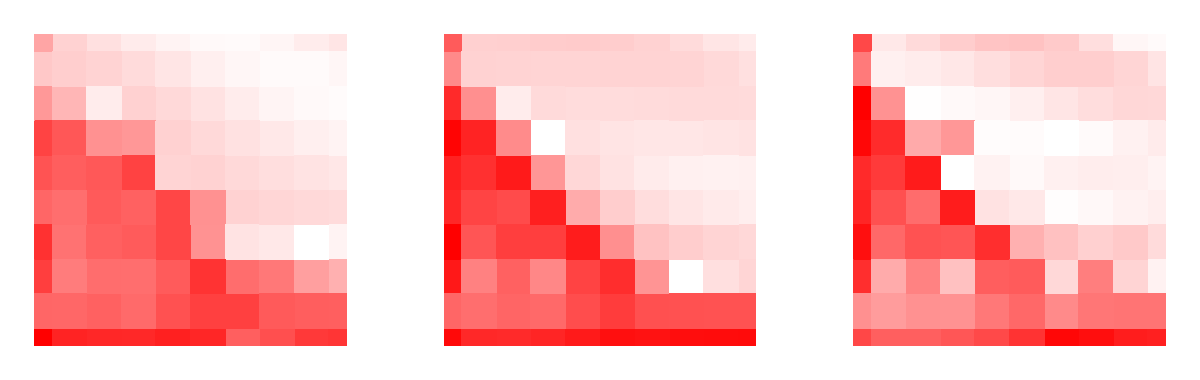

```mathematica
ftlePlot1=ListDensityPlot[kk1,InterpolationOrder->0,(*ColorFunction->CoolToWarm*)ColorFunction->Function[Blend[RGBColor@@@{RGBColor[1,1,1],Red},Slot[1]]],Frame->False,PlotRange->{All,All,All}];
ftlePlot6=ListDensityPlot[kk6,InterpolationOrder->0,(*ColorFunction->CoolToWarm*)ColorFunction->Function[Blend[RGBColor@@@{RGBColor[1,1,1],Red},Slot[1]]],Frame->False,PlotRange->{All,All,All}];
diffVals=Transpose[{Transpose[kk1][[1]],Transpose[kk1][[2]],Abs[(Transpose[kk1][[3]]/Median[Transpose[kk1][[3]]])-(Transpose[kk6][[3]]/Median[Transpose[kk6][[3]]])]}];
diffPlot=ListDensityPlot[diffVals,InterpolationOrder->0,(*ColorFunction->CoolToWarm*)ColorFunction->Function[Blend[RGBColor@@@{RGBColor[1,1,1],Red},Slot[1]]],Frame->False,PlotRange->{All,All,All}];
GraphicsRow[{ftlePlot1,ftlePlot6,diffPlot},ImageSize->Full]
```

```mathematica
kk1=ftleVals;
```

Why do the matrix powers not always have max eigenvalues that are powers of eachother
The issue is the working precision; we are dealing with numbers that easily reach 25 sig figs. How to deal with this? Maybe rescale the matrix before taking eigenvalues?

```mathematica
N[kk1^6,20]-kk2
```

{0.,-262144.,0.,1.07374×10^9,-327680.,9.53674×10^-6,-5.68434×10^-14,4.54747×10^-13,-2.72848×10^-12,-2.18279×10^-11,-65536.,-256.,-16.,2.,-2.32831×10^-10,4.54747×10^-13,-2.84217×10^-14,1.13687×10^-13,1.81899×10^-12,7.27596×10^-12,0.,64.,0.,-0.0000305176,0.,-7.10543×10^-15,-1.42109×10^-14,1.13687×10^-13,2.72848×10^-12,-5.45697×10^-12,3.35544×10^7,48.,0.,7.27596×10^-12,1.13687×10^-13,7.10543×10^-15,-4.26326×10^-14,-2.27374×10^-13,-4.54747×10^-12,4.54747×10^-13,6.71089×10^7,40.,-1.42109×10^-14,1.81899×10^-12,-7.10543×10^-15,2.66454×10^-15,5.68434×10^-14,2.27374×10^-13,-4.54747×10^-13,-5.68434×10^-14,6.71089×10^7,20.,-2.27374×10^-13,-4.54747×10^-13,7.10543×10^-15,5.32907×10^-15,2.84217×10^-14,9.09495×10^-13,3.41061×10^-13,-7.10543×10^-15,-1.34218×10^8,32.,-1.81899×10^-12,2.27374×10^-13,0.,3.55271×10^-15,-1.42109×10^-13,1.13687×10^-13,-2.84217×10^-14,-3.55271×10^-15,4.02653×10^8,-16.,1.81899×10^-12,-1.13687×10^-13,1.77636×10^-15,1.06581×10^-14,8.52651×10^-14,1.98952×10^-13,-3.55271×10^-15,0.,-2.68435×10^8,0.,3.63798×10^-12,0.,1.33227×10^-15,1.42109×10^-14,2.84217×10^-14,-2.84217×10^-14,-1.77636×10^-15,-1.42109×10^-14,-1.67772×10^8,-4.,0.,-1.98952×10^-13,-1.33227×10^-15,1.42109×10^-14,7.10543×10^-14,7.10543×10^-15,-1.77636×10^-15,-1.42109×10^-14}

```mathematica
Median[Transpose[ff6][[3]]]
Median[Transpose[fff6][[3]]^6]
```

56.8232

1012.35

```mathematica
Median[Transpose[fff][[3]]]
Median[Transpose[fff2][[3]]]
Median[Transpose[fff3][[3]]]
Median[Transpose[fff6][[3]]]
```

7.50131

6.20214

4.75446

3.16852

```mathematica
Median[Transpose[ff][[3]]]
Median[Transpose[ff2][[3]]]
Median[Transpose[ff3][[3]]]
Median[Transpose[ff6][[3]]]
```

7.50131

6.48336

5.82207

56.8232

```mathematica
compareVecs[vec1_,vec2_]:=vec1/Median[vec1]-vec2/Median[vec2];
```

```mathematica
Total[compareVecs[ff[[3]],ff2[[3]]]^2]
```

379.933

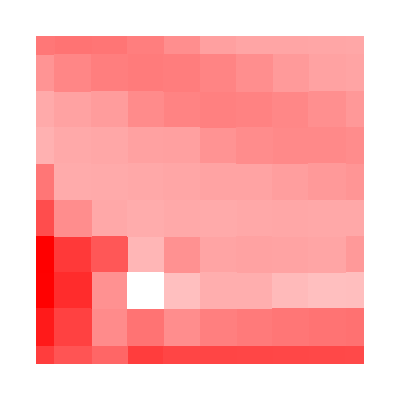

```mathematica
diffVals=Transpose@Join[Transpose[startPts],{ff[[3]]/Median[ff[[3]]]-ff6[[3]]/Median[ff6[[3]]]}];
ftlePlot=ListDensityPlot[diffVals,InterpolationOrder->0,(*ColorFunction->CoolToWarm*)ColorFunction->Function[Blend[RGBColor@@@{Red,RGBColor[1,1,1]},Slot[1]]],Frame->False,PlotRange->{All,All,All}]
```

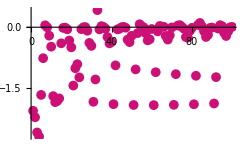

```mathematica
ListPlot[ff[[3]]-ff6[[3]]]
```

```mathematica
ff6=Transpose[ftleVals];
```

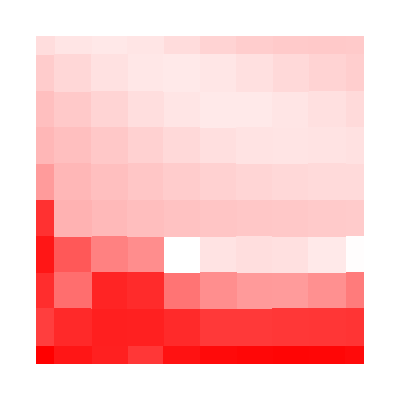

```mathematica
ftlePlot=ListDensityPlot[ftleVals,InterpolationOrder->0,(*ColorFunction->CoolToWarm*)ColorFunction->Function[Blend[RGBColor@@@{RGBColor[1,1,1],Red},Slot[1]]],Frame->False,PlotRange->{All,All,All}]
ftleVals;
```

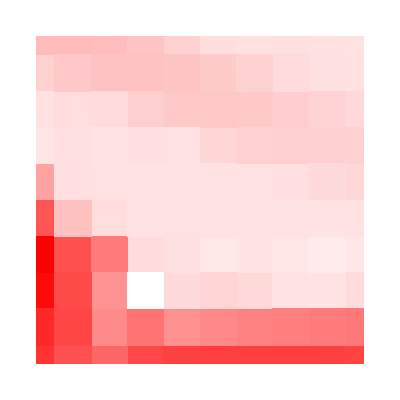

```mathematica
ftlePlot=ListDensityPlot[ftleVals,InterpolationOrder->0,(*ColorFunction->CoolToWarm*)ColorFunction->Function[Blend[RGBColor@@@{RGBColor[1,1,1],Red},Slot[1]]],Frame->False,PlotRange->{All,All,All}]
ftleVals;
```

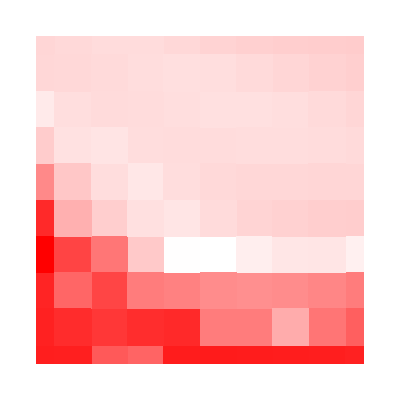

```mathematica
ftlePlot=ListDensityPlot[ftleVals,InterpolationOrder->0,(*ColorFunction->CoolToWarm*)ColorFunction->Function[Blend[RGBColor@@@{RGBColor[1,1,1],Red},Slot[1]]],Frame->False,PlotRange->{All,All,All}]
ftleVals;
```

```mathematica
messages={}
clearMessages[]:=messages={}
collectMessages[m_]:=AppendTo[messages,m]
Internal`AddHandler["Message",collectMessages]
(*Internal`RemoveHandler["Message",collectMessages]*)
```

{}

## Test case

```mathematica
Clear[testIntegrator]
```

```mathematica
Delete[testIntegrator];
testIntegrator[ v_]:=
Module[
	{vSub,odes,vp},
	vSub=(v/.{x->x[t]});
	odes={
	x'[t]==vSub,
	x[0]==x0
	};
	vp=x[t]/.ParametricNDSolve[
	odes,
	x[t],
	{t,0,1},
	{x0}];
	vp
]
```

/Users/william/Documents/Research/fluid mathematica package

testIntegrator::shdw: Symbol testIntegrator appears in multiple contexts {testPackage`,Global`}; definitions in context testPackage` may shadow or be shadowed by other definitions.

ParametricFunction[<>]

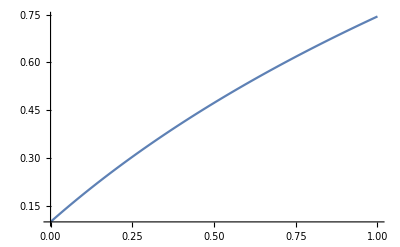

```mathematica
SetDirectory[NotebookDirectory[]]
<<testPackage.wl
pf=testIntegrator[Exp[-x],x,t]
Plot[pf[.1],{t,0,1}]
```

```mathematica
(*
buildIntegrator[ v_,tMax_]:=
Module[
{vSub,odes,vp},
vSub=(v/.{x->x[t],y->y[t]});
odes={x'[t]==vSub[[1]],y'[t]==vSub[[2]],x[0]==x0,y[0]==y0};
vp={x,y}/.ParametricNDSolve[
odes,
{x,y},
{t,0,tMax},{x0,y0}];
vp
]*)
SetDirectory[NotebookDirectory[]]
<<findFTLE.wl
dd={vx[t,x,y],vy[t,x,y]}/.params;
pf=buildIntegrator[dd,5,x,y,t,x0,y0]
pf[[1]][.1,.1][4]
```

/Users/william/Documents/Research/fluid mathematica package

ReplaceAll::reps: {params} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{ParametricFunction[<>],ParametricFunction[<>]}

ParametricNDSolve::ndnum: Encountered non-numerical value for a derivative at t$2346 == 0..

ParametricFunction[<>][0.1,0.1][4]

```mathematica
allFuncs[t_]:=kq[#[[1]],#[[2]],t]&/@N@makeMesh[{0,2},{-1,1},10,10];
ParametricPlot[allFuncs[t],{t,0,2}, AspectRatio->Automatic]
```

$Aborted

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

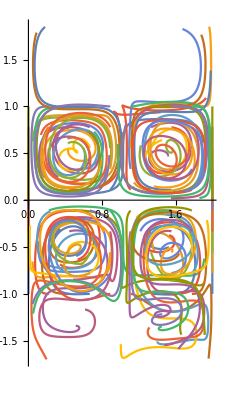

```mathematica
Options[streamPlot3] =Options[ParametricPlot];
streamPlot3[ seedPoints_,vfield_,timeLimit_,opts:OptionsPattern[streamPlot3]]:=(
(*
seedPoints : N-ist of 2-Lists;
	A list of starting points at which to initialize trajectories;

vfield : Pair of functions in x,y;
	Cartesian expression of a 2D vector field;

timeLimit : Real;
	The amount of time to integrate;
*)
seedRules={x0->#[[1]],y0->#[[2]]}&/@seedPoints;
memo1[x,y,t]:=vfield[[1]];
memo2[x,y,t]:=vfield[[2]];
s=NDSolve[{x'[t]==memo1[x[t],y[t],t],y'[t]==memo2[x[t],y[t],t],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,timeLimit}]/.seedRules;
ParametricPlot[Evaluate[{x[t],y[t]}/.s],{t,0,timeLimit},opts]
);

streamPlot3[makeMesh[{0,2},{-1,1},10,10],{vx[t,x,y],vy[t,x,y]}/.params,10]
```